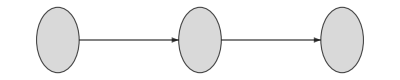

Set::write: Tag Inherited in Inherited[State] is Protected.

```mathematica
Graph[{A->B, B->C},VertexSize->0.3,VertexCoordinates->{A->{0,0},B->{2,0}, C->{4,0}},VertexLabels->Placed[Automatic,Center],
VertexStyle->LightGray,EdgeStyle->{Style,{Thick, Black}}]
```

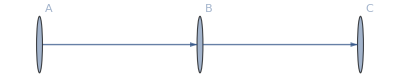

```mathematica
Graph[{{A,B}->C},VertexCoordinates->{{A,B}->{0,0},C->{2,0}},VertexLabels->Automatic]
```

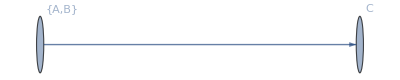

```mathematica
Graph[{A->{B,C}},VertexCoordinates->{A->{0,0},{B,C}->{2,0}},VertexLabels->Automatic]
```

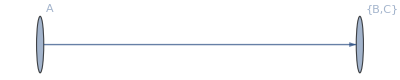

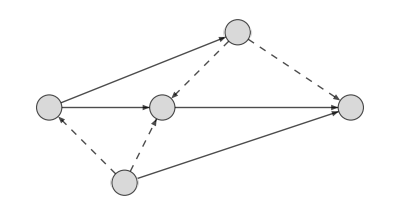

Set::write: Tag Inherited in Inherited[State] is Protected.

```mathematica
Graph[{A->B, B->C, A-> "(B, C)","(A, B)"->C,"(B, C)"->B,"(B, C)"->C,"(A, B)"->A,"(A, B)"->B},VertexCoordinates->{A->{0,0},B->{1.5,0},C->{4,0},"(B, C)"->{2.5,1},"(A, B)"->{1,-1}},
VertexSize->0.3,
VertexStyle->LightGray,
EdgeStyle->{Style, {Thick, Black},
"(A, B)"->A->Dashed,
"(A, B)"->B->Dashed, 
"(B, C)"->B->Dashed,"(B, C)"->C->Dashed
},
VertexLabels->Placed[Automatic, Center]]
```

```mathematica
Graph[{1->2, 2->3, 1-> 4,5->3,4->2,4->3,5->1,5->2,4->1,3->5},VertexCoordinates->{1->{0,0},2->{2,0},3->{4,0},4->{3,1
},5->{1,-1}},
VertexLabels->{1->"A",2->"B", 3->"C",4->"(B, C)",5->"(A, B)"},EdgeStyle->{4->1->Red}]
```

```mathematica
Graph[{1->2,2->3,1->4,5->3,4->2,4->3,5->1,5->2,4->1,3->5},VertexCoordinates->{1->{0,0},2->{2,0},3->{4,0},4->{3,1},5->{1,-1}},VertexLabels->{1->"A",2->"B",3->"C",4->"(B, C)",5->"(A, B)"},EdgeStyle->{4->1->RGBColor[1, 0, 0],3dede5->Red}]
```

```mathematica
Graph[{1->2,2->3,1->4,5->3,4->2,4->3,5->1,5->2,4->1,3->5},VertexCoordinates->{1->{0,0},2->{2,0},3->{4,0},4->{3,1},5->{1,-1}},VertexLabels->{1->"A",2->"B",3->"C",4->"(B, C)",5->"(A, B)"},EdgeStyle->{1->2->Green,2->3->Green,5->3->Green,1->5->Green,4->1->RGBColor[1, 0, 0],3 ->5->RGBColor[1, 0, 0], {Thick}}]
```

```mathematica
Graph[{1->2,2->3,1->4,5->3,4->2,4->3,5->1,5->2,4->1,3->5},VertexCoordinates->{1->{0,0},2->{2,0},3->{4,0},4->{3,1},5->{1,-1}},VertexLabels->{1->"A",2->"B",3->"C",4->"(B, C)",5->"(A, B)"},EdgeStyle->{1->2->RGBColor[0, 1, 0],2->3->RGBColor[0, 1, 0],5->3->RGBColor[0, 1, 0],1->4->RGBColor[0, 1, 0],4->1->RGBColor[1, 0, 0],3->5->RGBColor[1, 0, 0],5->1->Black,3->2->Black{Thickness[Large]}}]
```

```mathematica
Graph[{1->2,2->3,1->4,5->3,4->2,4->3,5->1,5->2,4->1,3->5},VertexCoordinates->{1->{0,0},2->{2,0},3->{4,0},4->{3,1},5->{1,-1}},VertexLabels->{1->"A",2->"B",3->"C",4->"(B, C)",5->"(A, B)"},EdgeStyle->{1->2->RGBColor[0, 1, 0],2->3->RGBColor[0, 1, 0],5->3->RGBColor[0, 1, 0],1->4->RGBColor[0, 1, 0],4->1->RGBColor[1, 0, 0],3->5->RGBColor[1, 0, 0],5->1->GrayLevel[0],3->2->GrayLevel[0] ,{Thickness[Large]}}]
```

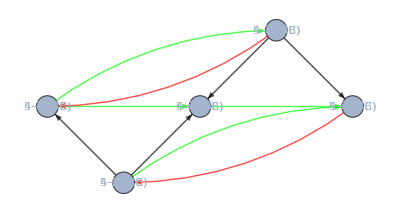

```mathematica
Graph[{1->2,2->3,1->4,5->3,4->2,4->3,5->1,5->2,4->1,3->5},VertexCoordinates->{1->{0,0},2->{2,0},3->{4,0},4->{3,1},5->{1,-1}},VertexLabels->Placed[{1->"A",2->"B",3->"C",4->"(B, C)",5->"(A, B)"},Center],
VertexSize->0.2,EdgeStyle->{1->2->RGBColor[0, 1, 0],2->3->RGBColor[0, 1, 0],5->3->RGBColor[0, 1, 0],1->4->RGBColor[0, 1, 0],4->1->RGBColor[1, 0, 0],3->5->RGBColor[1, 0, 0],5->1->GrayLevel[0],5->2->GrayLevel[0],4->2->Black,4->3->Black,{Thickness[Large]}},
EdgeStyle->{5->1->Dashed,5->2->Dashed,{Thick}}]
```

```mathematica
Graph[{"A"->"B","B"->"C","A"->"(B, C)","(A, B)"->"C","(B, C)"->"C"},VertexCoordinates->{"A"->{0,0},"B"->{2,0},"C"->{4,0},"(B, C)"->{3,1},"(A, B)"->{1,-1}},VertexLabels->Placed[Automatic,Center],
VertexSize->0.2,EdgeStyle->{1->2->RGBColor[0, 1, 0],2->3->RGBColor[0, 1, 0],5->3->RGBColor[0, 1, 0],1->4->RGBColor[0, 1, 0],4->1->RGBColor[1, 0, 0],3->5->RGBColor[1, 0, 0],5->1->GrayLevel[0],5->2->GrayLevel[0],4->2->Black,4->3->Black,{Thickness[Large]}},
EdgeStyle->{5->1->Dashed,5->2->Dashed,{Thick}}]
```

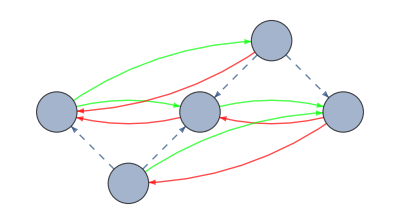

```mathematica
Graph[{"A"->"B","B"->"C","A"->"(B, C)","(A, B)"->"C","(B, C)"->"B","(B, C)"->"C","(A, B)"->"A", "(A, B)"->"B","(B, C)"->"A","C"->"(A, B)","C"->"B", "B"->"A"}, VertexCoordinates->{"A"->{0,0},"B"->{2,0},"C"->{4,0},"(B, C)"->{3,1},"(A, B)"->{1,-1}},VertexLabels->Placed[Automatic,Center],VertexSize->0.4,EdgeStyle->{"A"->"B"->RGBColor[0, 1, 0],"B"->"C"->RGBColor[0, 1, 0],"(A, B)"->"C"->Green,"A"->"(B, C)"->Green,"(B, C)"->"C"->Dashed,"(B, C)"->"B"->Dashed,"(A, B)"->"A"->Dashed,"(A, B)"->"B"->Dashed,"(B, C)"->"A"->Red,"C"->"(A, B)"-> Red,"B"->"A"->Red,
"C"->"B"->Red,Thickness[Large]}]
```

```mathematica
h[{A->B, B->C},VertexCoordinates->{A->{0,0},B->{1,0}, C->{2,0}},VertexLabels->Placed[Automatic,Center]]
```

h[{A->B,B->C},VertexCoordinates→{A→{0,0},B→{1,0},C→{2,0}},VertexLabels→Placed[Automatic,Center]]

```mathematica
Graph[
{A->B,
B->C,
"(A, B)"->A,
"(A, B)"->B,
"(A, B)"->C,
"(B, C)"->B,
"(B, C)"->C,
"(B, C)"->A},
VertexLabels->Placed[Automatic,Center],
VertexSize->0.7,
VertexStyle->LightGray,VertexLabels->Placed[Automatic,Center],
VertexCoordinates->{"A"->{1,2},"B"->{1,0},"C"->{2,0}},
EdgeStyle->{Style,{Thick, Black},"(B, C)"->A->Dotted,"(B, C)"->B->Dotted,"(A, B)"->A->Dotted,"(A, B)"->B->Dotted}]
```

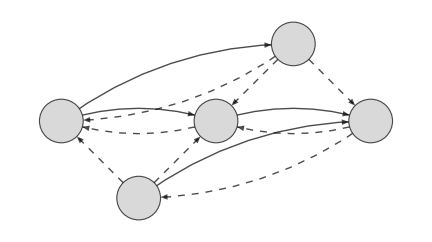

Set::write: Tag Inherited in Inherited[State] is Protected.

```mathematica
Graph[{"A"->"B","B"->"C","A"->"(B, C)","(A, B)"->"C","(B, C)"->"B","(B, C)"->"C","(A, B)"->"A", "(A, B)"->"B","(B, C)"->"A","C"->"(A, B)","C"->"B", "B"->"A"}, VertexCoordinates->{"A"->{0,0},"B"->{2,0},"C"->{4,0},"(B, C)"->{3,1},"(A, B)"->{1,-1}},VertexLabels->Placed[Automatic,Center],VertexSize->0.4,VertexStyle->LightGray,EdgeStyle->{Style,{Thick, Black},"(A, B)"->"A"->Dashed,"(A, B)"->"B"->Dashed,
"(B, C)"->"B"->Dashed,"(B, C)"->"C"->Dashed,
"C"->"B"->Dashed,"C"->"(A, B)"->Dashed,
"(B, C)"->"A"->Dashed,"B"->"A"->Dashed}]
```

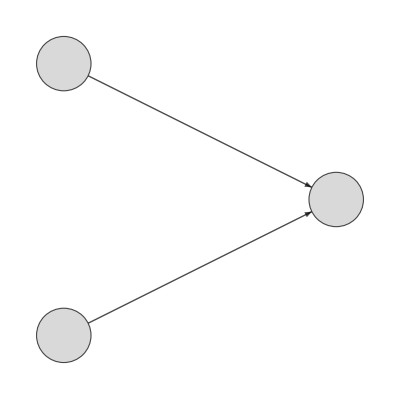

Set::write: Tag Inherited in Inherited[State] is Protected.

```mathematica
Graph[{"A"->"C","B"->"C"}, VertexCoordinates->{"A"->{0,0.5},"B"->{0,-0.5},"C"->{1,0}},
VertexLabels->Placed[Automatic,Center],VertexSize->0.2,
EdgeStyle->{Style, {Thick, Black}},
VertexShapeFunction->"Circle",
VertexStyle->{LightGray},
GraphLayout->"SpringEmbedding"]
```

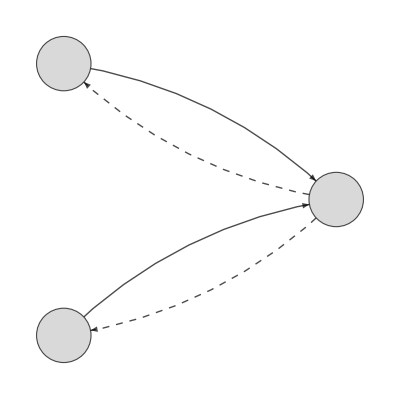

Set::write: Tag Inherited in Inherited[State] is Protected.

```mathematica
Graph[{"A"->"C","B"->"C","C"->"A","C"->"B"}, VertexCoordinates->{"A"->{0,0.5},"B"->{0,-0.5},"C"->{1,0}},
VertexLabels->Placed[Automatic,Center],VertexSize->0.2,
EdgeStyle->{Style, {Thick, Black},"C"->"B"->Dashed,"C"->"A"->Dashed},
VertexShapeFunction->"Circle",
VertexStyle->{LightGray},
GraphLayout->"SpringEmbedding"]
```

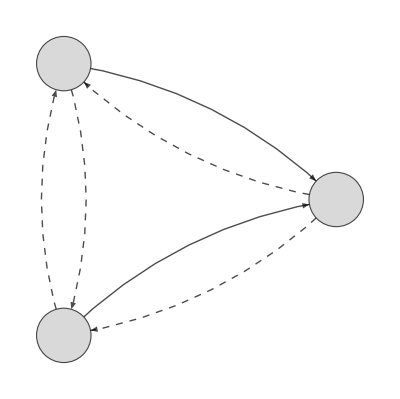

Set::write: Tag Inherited in Inherited[State] is Protected.

```mathematica
Graph[{"A"->"C","B"->"C","C"->"A","C"->"B","A"->"B","B"->"A"}, VertexCoordinates->{"A"->{0,0.5},"B"->{0,-0.5},"C"->{1,0}},
VertexLabels->Placed[Automatic,Center],VertexSize->0.2,
VertexShapeFunction->"Circle",
VertexStyle->{LightGray},
EdgeStyle->{Style, {Thick, Black},
"A"->"B"->Dashed,
"B"->"A"->Dashed,"C"->"B"->Dashed,"C"->"A"->Dashed},
GraphLayout->"SpringEmbedding"]
```

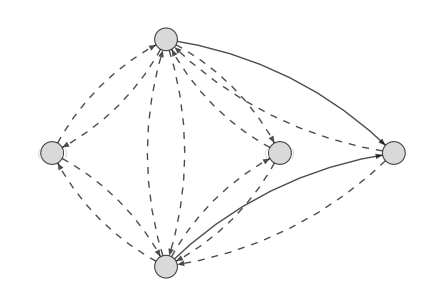

Set::write: Tag Inherited in Inherited[State] is Protected.

```mathematica
Graph[{"A"->"C","B"->"C","C"->"A","C"->"B","A"->"B","B"->"A",
"(A; B)"->"A","A"->"(A; B)",
"(A; B)"->"B","B"->"(A; B)",
"A"->"(B; A)",
"(B; A)"->"A","(B; A)"->"B", "B"->"(B; A)"}, VertexCoordinates->{"A"->{0,0.5},"B"->{0,-0.5},"C"->{1,0},"(A; B)"->{-0.5, 0},"(B; A)"->{0.5, 0}},
VertexLabels->Placed[Automatic,Center],VertexSize->0.2,
VertexShapeFunction->"Circle",
VertexStyle->{LightGray},
EdgeStyle->{Style, {Thick, Black},
"A"->"B"->Dashed,
"B"->"A"->Dashed, 
"(A; B)"->"A"->Dashed, 
"A"->"(B; A)"->Dashed,
"(B; A)"->"A"->Dashed, 
"A"->"(A; B)"->Dashed, 
"(A; B)"->"B"->Dashed,
"(B; A)"->"A"->Dashed, 
"(B; A)"->"B"->Dashed,
"A"->"(B; A)"->Dashed,
"B"->"(A; B)"->Dashed,"B"->"(B; A)"->Dashed,
"C"->"B"->Dashed,"C"->"A"->Dashed},
GraphLayout->"SpringEmbedding"]
```

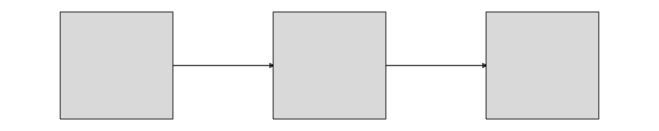

Set::write: Tag Inherited in Inherited[State] is Protected.

```mathematica
Graph[{"A"->"B","B"->"C"}, VertexCoordinates->{"A"->{0,0},"B"->{1,0},"C"->{2,0}},
VertexLabels->Placed[Automatic,Center],VertexSize->0.5,
EdgeStyle->{Style, {Thick, Black}},
VertexShapeFunction->"Rectangle",
VertexStyle->{LightGray},
GraphLayout->"SpringEmbedding"]
```

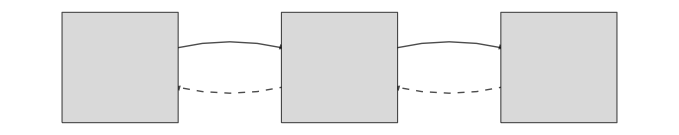

```mathematica
Graph[{"A"->"B","B"->"C","C"->"B","B"->"A"}, VertexCoordinates->{"A"->{0,0},"B"->{1,0},"C"->{2,0}},
VertexLabels->Placed[Automatic,Center],VertexSize->0.5,
EdgeStyle->{Style, {Thick, Black},
"C"->"B"->Dashed,
"B"->"A"->Dashed},
VertexShapeFunction->"Rectangle",
VertexStyle->{LightGray},
GraphLayout->"SpringEmbedding"]
```

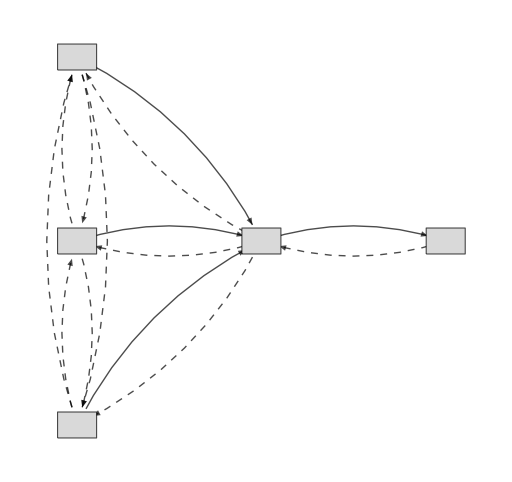

Set::write: Tag Inherited in Inherited[State] is Protected.

```mathematica
Graph[
{"S_d1"->"R","S_d2"->"R","S_d3"->"R",
"R"->"Sr","Sr"->"R",
"R"->"S_d1",
"R"->"S_d2",
"R"->"S_d3",
"S_d1"->"S_d2",
"S_d2"->"S_d1",
"S_d1"->"S_d3",
"S_d3"->"S_d1",
"S_d2"->"S_d3",
"S_d3"->"S_d2"}, 
VertexCoordinates->
{"S_d1"->{0,1},
"S_d2"->{0,0},
"S_d3"->{0,-1},
"R"->{1,0},
"Sr"->{2,0}},
VertexLabels->Placed[Automatic,Center],VertexSize->0.2,
EdgeStyle->{Style, {Thick, Black},
"S_d1"->"S_d2"->Dashed,
"S_d2"->"S_d1"->Dashed,
"S_d2"->"S_d3"->Dashed,
"S_d3"->"S_d2"->Dashed,
"S_d1"->"S_d3"->Dashed,
"S_d3"->"S_d1"->Dashed,
"R"->"S_d3"->Dashed,
"R"->"S_d2"->Dashed,
"R"->"S_d1"->Dashed,
"Sr"->"R"->Dashed
},
VertexStyle->{LightGray},
VertexShapeFunction->"Rectangle",
GraphLayout->"SpringEmbedding"]
```

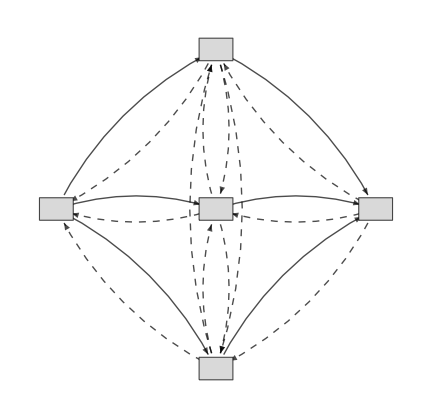

Set::write: Tag Inherited in Inherited[State] is Protected.

```mathematica
Graph[
{"Sd"->"R1",
"R1"->"Sr","Sr"->"R1",
"R2"->"Sr","Sr"->"R2",
"R3"->"Sr",
"Sd"->"R3",
"Sr"->"R3",
"R3"->"Sd",
"Sd"->"R2",
"R2"->"Sd",
"R1"->"Sd",
"R1"->"R2",
"R2"->"R1",
"R1"->"R3",
"R3"->"R1",
"R2"->"R3",
"R3"->"R2"}, 
VertexCoordinates->
{"Sd"->{0,0},
"R1"->{1,1},
"R2"->{1,0},
"R3"->{1,-1},
"Sr"->{2,0}},
VertexLabels->Placed[Automatic,Center],VertexSize->0.2,
EdgeStyle->{Style, {Thick, Black},
"R1"->"R2"->Dashed,
"R2"->"R1"->Dashed,
"R2"->"R3"->Dashed,
"R3"->"R2"->Dashed,
"R1"->"R3"->Dashed,
"R3"->"R1"->Dashed,
"Sr"->"R1"->Dashed,"Sr"->"R2"->Dashed,"Sr"->"R3"->Dashed,
"R1"->"Sd"->Dashed,"R2"->"Sd"->Dashed,"R3"->"Sd"->Dashed
},
VertexStyle->{LightGray},
VertexShapeFunction->"Rectangle",
GraphLayout->"SpringEmbedding"]
```

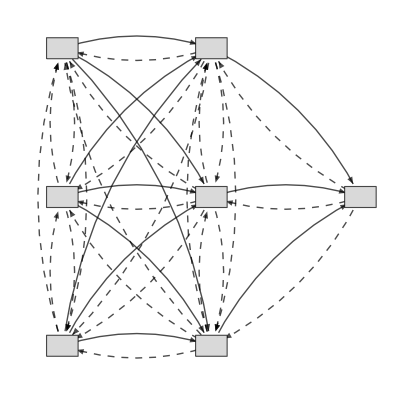

Set::write: Tag Inherited in Inherited[State] is Protected.

```mathematica
Graph[
{"Sd1"->"R1",
"Sd1"->"Sd2",
"Sd2"->"Sd1",
"Sd2"->"R1",
"Sd2"->"Sd3",
"Sd2"->"R2",
"Sd2"->"R3",
"Sd3"->"R1",
"Sd3"->"Sd2",
"Sd3"->"R2",
"Sd3"->"R3",
"R1"->"Sd2",
"R1"->"Sd3",
"R3"->"Sd3",
"R3"->"Sd2",
"R1"->"Sr","Sr"->"R1",
"R2"->"Sr","Sr"->"R2",
"R3"->"Sr",
"Sd1"->"R3",
"Sd1"->"Sd3",
"Sd3"->"Sd1",
"Sr"->"R3",
"R3"->"Sd1",
"Sd1"->"R2",
"R2"->"Sd1",
"R2"->"Sd2",
"R1"->"Sd1",
"R1"->"R2",
"R2"->"R1",
"R1"->"R3",
"R3"->"R1",
"R2"->"R3",
"R2"->"Sd3",
"R3"->"R2"}, 
VertexCoordinates->
{"Sd1"->{0,1},
"Sd2"->{0,0},
"Sd3"->{0,-1},
"R1"->{1,1},
"R2"->{1,0},
"R3"->{1,-1},
"Sr"->{2,0}},
VertexLabels->Placed[Automatic,Center],VertexSize->0.2,
EdgeStyle->{Style, {Thick, Black},
"R1"->"R2"->Dashed,
"R2"->"R1"->Dashed,
"R2"->"R3"->Dashed,
"R3"->"R2"->Dashed,
"R1"->"R3"->Dashed,
"R3"->"R1"->Dashed,
"Sd1"->"Sd2"->Dashed,
"Sd2"->"Sd1"->Dashed,
"Sd2"->"Sd3"->Dashed,
"Sd3"->"Sd2"->Dashed,"Sd3"->"Sd1"->Dashed,"Sd1"->"Sd3"->Dashed,
"Sr"->"R2"->Dashed,"Sr"->"R1"->Dashed,"Sr"->"R3"->Dashed,
"R1"->"Sd1"->Dashed,"R1"->"Sd2"->Dashed,"R1"->"Sd3"->Dashed,
"R2"->"Sd1"->Dashed,"R2"->"Sd2"->Dashed,"R2"->"Sd3"->Dashed,
"R3"->"Sd1"->Dashed,"R3"->"Sd2"->Dashed,"R3"->"Sd3"->Dashed},
VertexStyle->{LightGray},
VertexShapeFunction->"Rectangle",
GraphLayout->"SpringEmbedding"]
```